High-energy radiation and pair production by Coulomb processes in particle-in-cell simulations

B. Martinez, M. Lobet, R. Duclous, et al. Phys. Plasmas 26, 103109 (2019)
Notebook: Óscar Amaro, February 2023 @ GoLP-EPP

Introduction
In this notebook we reproduce some results from the paper.
Also, see https://github.com/bertrandmartinez/benchmark_osiris_qed for Python scripts to produce QED-Coulomb rates.

## Fig 2

```mathematica
Clear[Γc,g,L,Lbar,δpp,δpm,η]
Clear[αf,e,ϵ0,ℏ,c,re,me,rc,Lbar,δ]
αf=e^2/(4π ϵ0 ℏ c);
re=e^2/(4π ϵ0 me c^2);

I1=Lbar δ (ArcTan[δ Lbar]-ArcTan[Lbar])-Lbar^2/2(1-δ)^2/(1+Lbar^2)+1/2 Log[(1+Lbar^2)/(1+Lbar^2 δ^2)];
I2=1/2(4Lbar^3 δ^3(ArcTan[Lbar δ]-ArcTan[Lbar])+(1+3Lbar^2 δ^2)Log[(1+Lbar^2)/(1+Lbar^2 δ^2)]+(6Lbar^4 δ^2)/(1+Lbar^2)Log[δ]+(Lbar^2(δ-1)(δ+1-4Lbar^2 δ^2))/(1+Lbar^2));
dσBrnrTFDdk = (16re^2Z^2  αf)/(3k p1^2)(g[δpp,δpm,ηTF,LTF])(*eq 8*)
```

(e^6 Z^2 g[δpp,δpm,ηTF,LTF])/(12 c^5 k me^2 p1^2 π^3 ϵ0^3 ℏ)

```mathematica
Clear[Γc,g,L,Lbar,δpp,δpm,η]
Clear[αf,e,ϵ0,ℏ,c,re,me,rc,Lbar,δ]
αf=e^2/(4π ϵ0 ℏ c);
re=e^2/(4π ϵ0 me c^2);

I1=Lbar δ (ArcTan[δ Lbar]-ArcTan[Lbar])-Lbar^2/2(1-δ)^2/(1+Lbar^2)+1/2 Log[(1+Lbar^2)/(1+Lbar^2 δ^2)];
I2=1/2(4Lbar^3 δ^3(ArcTan[Lbar δ]-ArcTan[Lbar])+(1+3Lbar^2 δ^2)Log[(1+Lbar^2)/(1+Lbar^2 δ^2)]+(6Lbar^4 δ^2)/(1+Lbar^2)Log[δ]+(Lbar^2(δ-1)(δ+1-4Lbar^2 δ^2))/(1+Lbar^2));
dσBrrTFDdk = (4Z^2 re^2 αf)/k((1+((γ1-k)/γ1)^2)(I1+1)-2/3(γ1-k)/γ1(I2+5/6))(*eq 12*)
```

1/(16 c^5 k me^2 π^3 ϵ0^3 ℏ)e^6 Z^2 ((1+(-k+γ1)^2/γ1^2) (1-(Lbar^2 (1-δ)^2)/(2 (1+Lbar^2))+Lbar δ (-ArcTan[Lbar]+ArcTan[Lbar δ])+1/2 Log[(1+Lbar^2)/(1+Lbar^2 δ^2)])-1/(3 γ1)2 (-k+γ1) (5/6+1/2 ((Lbar^2 (-1+δ) (1+δ-4 Lbar^2 δ^2))/(1+Lbar^2)+4 Lbar^3 δ^3 (-ArcTan[Lbar]+ArcTan[Lbar δ])+(6 Lbar^4 δ^2 Log[δ])/(1+Lbar^2)+(1+3 Lbar^2 δ^2) Log[(1+Lbar^2)/(1+Lbar^2 δ^2)])))

## Fig 5

```mathematica
Clear[Γc,g,L,Lbar,δpp,δpm,η]
Clear[αf,e,ϵ0,ℏ,c,re,me,rc]
αf=e^2/(4π ϵ0 ℏ c);
re=e^2/(4π ϵ0 me c^2);


Γc=(ηTF ηD)/(LbarD-LbarTF^2)(()^2 Log[])
g[δpp,δpm,η,L]:=η^2/2(Log[(δpp Lbar^2+1)/(δpm Lbar^2+1)]+1/(δpp Lbar^2+1)-1/(δpm Lbar^2+1))
```

## Fig 8 Bethe-Heitler cross section

```mathematica
Clear[Γc,g,L,Lbar,δpp,δpm,η]
Clear[αf,e,ϵ0,ℏ,c,re,me,rc,γp,γm]
αf=e^2/(4π ϵ0 ℏ c);
re=e^2/(4π ϵ0 me c^2);

γm=k-γp;
δ=k/(2γp γm);

dσBHdγp=(4Z^2 re^2 αf)/k^3((γp^2+γm^2)(I1+1)+2/3 γp γm(I2+5/6));
Plot[dσBHdγp,{γpk,0,1}];
```

## Equation 21 > 22

```mathematica
Clear[a,x,eq]
eq=2a(x+1)-(x+1)Log[x+1]+x
Solve[eq==0,x]

res=eq/.{x->Exp[ProductLog[-Exp[-1-2a]+1+2a]-1]}//FullSimplify
Refine[res,{a>0}]//Simplify
```

x+2 a (1+x)-(1+x) Log[1+x]

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[x+2 a (1+x)-(1+x) Log[1+x]==0,x]

1/ⅇ(ⅇ+2 a ⅇ+2 (1+a) ⅇ^ProductLog[1+2 a-ⅇ^(-1-2 a)]-(ⅇ+ⅇ^ProductLog[1+2 a-ⅇ^(-1-2 a)]) Log[ⅇ+ⅇ^ProductLog[1+2 a-ⅇ^(-1-2 a)]])

1/ⅇ(ⅇ+2 a ⅇ+2 (1+a) ⅇ^ProductLog[1+2 a-ⅇ^(-1-2 a)]-(ⅇ+ⅇ^ProductLog[1+2 a-ⅇ^(-1-2 a)]) Log[ⅇ+ⅇ^ProductLog[1+2 a-ⅇ^(-1-2 a)]])

## Fig 9

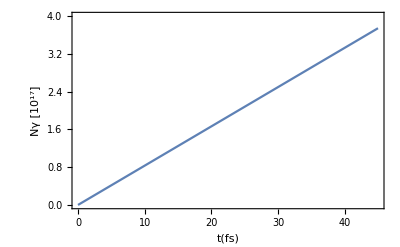

```mathematica
Clear[Nγ,ne,ni,νe,l,σB,t,dNγdk,dσBdk]

(* what are the values of νe, σB, dσB/dk ? *)
l = 1.6 10^-6;(*[m]*)
ne=10^21 10^6;(*[m^-3]*)
ni=8 10^22 10^6;(*[m^-3]*)

(* eq 38 *)
Nγ=ne ni νe l σB t;
(* eq 39 *)
dNγdk=ne ni νe l dσBdk t;

Plot[10^-19 Nγ/.{t->tfs 10^-15,νe->0.65 10^-17,σB->1},{tfs,0,45},PlotRange->{0,4},Frame->True,FrameLabel->{"t(fs)","Nγ [10^17]"}]

(* how to use k/(γe-1) for fig 9b? *)
```

## Appendix D: Useful Indefinite Integrals

```mathematica
Clear[u,L,Lα,Lβ]

(* D1 *)
res=Integrate[u^3/((1+L^2 u^2)^2),u]//Simplify;
res-1/(2 L^4)(Log[1+L^2 u^2]+1/(1+L^2 u^2))//Simplify

(* D2 *)
res=Integrate[u^2/((1+L^2 u^2)^2),u]//Simplify;
res--1/(2 L^3)(-ArcTan[L u]+(L u)/(1+L^2 u^2))//Simplify

(* D3 *)
res=Integrate[u/((1+L^2 u^2)^2),u]//Simplify;
res--1/(2 L^2)(1/(1+L^2 u^2))//Simplify

(* D4 *)
res=Integrate[1/((1+L^2 u^2)^2),u]//Simplify;
res--1/(2 L^2)(-L ArcTan[L u]-1/u+1/(u(1+L^2 u^2)))//Simplify

(* D5 *)
res=Integrate[(u Log[u])/((1+L^2 u^2)^2),u]//Simplify;
res--1/(2 L^2)(Log[u]/(1+L^2 u^2)-Log[u]+1/2 Log[1+L^2 u^2])//Simplify

(* D6 *)
res=Integrate[u^3/((1+Lα^2 u^2)(1+Lβ^2 u^2)),u]//Simplify;
res-(Lα^2 Log[1+Lβ^2 u^2]-Lβ^2 Log[1+Lα^2 u^2])/(2 Lα^2 Lβ^2(Lα^2-Lβ^2))//Simplify
```

0

0

0

«3 more identical outputs»